```mathematica
Quit[]
```

## Setup

```mathematica
FR$Parallel=False;
$FeynRulesPath=SetDirectory["/Users/laramason/Downloads/feynrules-current"];
<<FeynRules`;
SetDirectory[$FeynRulesPath<>"/Models/Composite_Higgs"];
LoadModel["sm.fr","ch_ps.fr"];
LoadRestriction["DiagonalCKM.rst"] (*,"Massless.rst"]*)
```

- FeynRules -

Version: 2.3.32 ( 12 March 2018).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

args::shdw: Symbol args appears in multiple contexts {FeynRules`,Global`}; definitions in context FeynRules` may shadow or be shadowed by other definitions.

Merging model-files...

This model implementation was created by

L. Mason

B. Fuks

Model Version: 1.1

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model CHpseudo loaded.

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

## Lagrangian playground

In Feynman gauge: no ghosts and no goldstones

```mathematica
CheckMassSpectrum[LPSeudo+LSM]
```

```mathematica
CheckHermiticity[ExpandIndices[LPSeudo + LSM]/.{(G0|GP|GPbar)->0}]
```

```mathematica
WriteUFO[ExpandIndices[LPSeudo],ExpandIndices[LSM],AddDecays->False, Output->"CHPS_UFO_M1_kgeffp_new"]
```

## Calculation of branching ratios

```mathematica
vertices = FeynmanRules[LSM+LPSeudo]
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

126 possible non-zero vertices have been found -> starting the computation:  / 126.

117 vertices obtained.

{{{{G0,1},{G0,2},{G0,3},{G0,4}},-6 ⅈ lam},{{{G0,1},{G0,2},{GP,3},{GP^†,4}},-2 ⅈ lam},{{{GP,1},{GP,2},{GP^†,3},{GP^†,4}},-4 ⅈ lam},{{{G0,1},{G0,2},{H,3},{H,4}},-2 ⅈ lam},{{{GP,1},{GP^†,2},{H,3},{H,4}},-2 ⅈ lam},{{{H,1},{H,2},{H,3},{H,4}},-6 ⅈ lam},{{{G0,1},{G0,2},{H,3}},-2 ⅈ lam vev},{{{GP,1},{GP^†,2},{H,3}},-2 ⅈ lam vev},{{{H,1},{H,2},{H,3}},-6 ⅈ lam vev},{{{A,1},{A,2},{GP,3},{GP^†,4}},2 ⅈ e^2 η_(μ_1,μ_2)},{{{A,1},{GP,2},{GP^†,3}},ⅈ e p_2^μ_1-ⅈ e p_3^μ_1},{{{ghA^†,1},{ghWm,2},{W,3}},ⅈ e p_2^μ_3+ⅈ e p_3^μ_3},{{{ghA^†,1},{ghWp,2},{W^†,3}},-ⅈ e p_2^μ_3-ⅈ e p_3^μ_3},{{{ghWm^†,1},{ghA,2},{GP^†,3}},(e^2 vev)/(2 s_w)},{{{ghWm^†,1},{ghA,2},{W^†,3}},ⅈ e p_2^μ_3+ⅈ e p_3^μ_3},{{{ghWm^†,1},{ghWm,2},{G0,3}},-(e^2 vev)/(4 s_w^2)},{{{ghWm^†,1},{ghWm,2},{H,3}},-(ⅈ e^2 vev)/(4 s_w^2)},{{{ghWm^†,1},{ghWm,2},{A,3}},-ⅈ e p_2^μ_3-ⅈ e p_3^μ_3},{{{ghWm^†,1},{ghWm,2},{Z,3}},-(ⅈ c_w e p_2^μ_3)/s_w-(ⅈ c_w e p_3^μ_3)/s_w},{{{ghWm^†,1},{ghZ,2},{GP^†,3}},-(e^2 vev)/(4 c_w)+(c_w e^2 vev)/(4 s_w^2)},{{{ghWm^†,1},{ghZ,2},{W^†,3}},(ⅈ c_w e p_2^μ_3)/s_w+(ⅈ c_w e p_3^μ_3)/s_w},{{{ghWp^†,1},{ghA,2},{GP,3}},-(e^2 vev)/(2 s_w)},{{{ghWp^†,1},{ghA,2},{W,3}},-ⅈ e p_2^μ_3-ⅈ e p_3^μ_3},{{{ghWp^†,1},{ghWp,2},{G0,3}},(e^2 vev)/(4 s_w^2)},{{{ghWp^†,1},{ghWp,2},{H,3}},-(ⅈ e^2 vev)/(4 s_w^2)},{{{ghWp^†,1},{ghWp,2},{A,3}},ⅈ e p_2^μ_3+ⅈ e p_3^μ_3},{{{ghWp^†,1},{ghWp,2},{Z,3}},(ⅈ c_w e p_2^μ_3)/s_w+(ⅈ c_w e p_3^μ_3)/s_w},{{{ghWp^†,1},{ghZ,2},{GP,3}},(e^2 vev)/(4 c_w)-(c_w e^2 vev)/(4 s_w^2)},{{{ghWp^†,1},{ghZ,2},{W,3}},-(ⅈ c_w e p_2^μ_3)/s_w-(ⅈ c_w e p_3^μ_3)/s_w},{{{ghZ^†,1},{ghWm,2},{GP,3}},(e^2 vev)/(4 c_w)+(c_w e^2 vev)/(4 s_w^2)},{{{ghZ^†,1},{ghWm,2},{W,3}},(ⅈ c_w e p_2^μ_3)/s_w+(ⅈ c_w e p_3^μ_3)/s_w},{{{ghZ^†,1},{ghWp,2},{GP^†,3}},-(e^2 vev)/(4 c_w)-(c_w e^2 vev)/(4 s_w^2)},{{{ghZ^†,1},{ghWp,2},{W^†,3}},-(ⅈ c_w e p_2^μ_3)/s_w-(ⅈ c_w e p_3^μ_3)/s_w},{{{ghZ^†,1},{ghZ,2},{H,3}},-1/2 ⅈ e^2 vev-(ⅈ c_w^2 e^2 vev)/(4 s_w^2)-(ⅈ e^2 s_w^2 vev)/(4 c_w^2)},{{{A,1},{A,2},{eta,3}},-(ⅈ e^2 K_b ϵ_(μ_1,μ_2,mu$1,mu$2) p_1^mu$2 p_2^mu$1)/(8 f_a π^2)-(ⅈ e^2 K_w ϵ_(μ_1,μ_2,mu$1,mu$2) p_1^mu$2 p_2^mu$1)/(8 f_a π^2)+(ⅈ e^2 K_b ϵ_(μ_1,μ_2,mu$1,mu$2) p_1^mu$1 p_2^mu$2)/(8 f_a π^2)+(ⅈ e^2 K_w ϵ_(μ_1,μ_2,mu$1,mu$2) p_1^mu$1 p_2^mu$2)/(8 f_a π^2)},{{{eta,1},{W,2},{W^†,3}},-(ⅈ e^2 K_w ϵ_(μ_2,μ_3,mu$1,mu$2) p_2^mu$2 p_3^mu$1)/(8 f_a π^2 s_w^2)+(ⅈ e^2 K_w ϵ_(μ_2,μ_3,mu$1,mu$2) p_2^mu$1 p_3^mu$2)/(8 f_a π^2 s_w^2)},{{{A,1},{eta,2},{Z,3}},-(ⅈ c_w e^2 K_w ϵ_(μ_1,μ_3,mu$1,mu$2) p_1^mu$2 p_3^mu$1)/(8 f_a π^2 s_w)+(ⅈ e^2 K_b s_w ϵ_(μ_1,μ_3,mu$1,mu$2) p_1^mu$2 p_3^mu$1)/(8 c_w f_a π^2)+(ⅈ c_w e^2 K_w ϵ_(μ_1,μ_3,mu$1,mu$2) p_1^mu$1 p_3^mu$2)/(8 f_a π^2 s_w)-(ⅈ e^2 K_b s_w ϵ_(μ_1,μ_3,mu$1,mu$2) p_1^mu$1 p_3^mu$2)/(8 c_w f_a π^2)},{{{eta,1},{Z,2},{Z,3}},-(ⅈ c_w^2 e^2 K_w ϵ_(μ_2,μ_3,mu$1,mu$2) p_2^mu$2 p_3^mu$1)/(8 f_a π^2 s_w^2)-(ⅈ e^2 K_b s_w^2 ϵ_(μ_2,μ_3,mu$1,mu$2) p_2^mu$2 p_3^mu$1)/(8 c_w^2 f_a π^2)+(ⅈ c_w^2 e^2 K_w ϵ_(μ_2,μ_3,mu$1,mu$2) p_2^mu$1 p_3^mu$2)/(8 f_a π^2 s_w^2)+(ⅈ e^2 K_b s_w^2 ϵ_(μ_2,μ_3,mu$1,mu$2) p_2^mu$1 p_3^mu$2)/(8 c_w^2 f_a π^2)},{{{eta,1},{G,2},{G,3}},-(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,α1,β1) p_2^β1 p_3^α1 δ_(a_2,a_3))/(32 f_a π^2)-(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,α1,δ1) p_2^δ1 p_3^α1 δ_(a_2,a_3))/(32 f_a π^2)+(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,α1,β1) p_2^α1 p_3^β1 δ_(a_2,a_3))/(32 f_a π^2)+(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,γ1,β1) p_2^γ1 p_3^β1 δ_(a_2,a_3))/(32 f_a π^2)-(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,γ1,β1) p_2^β1 p_3^γ1 δ_(a_2,a_3))/(32 f_a π^2)-(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,γ1,δ1) p_2^δ1 p_3^γ1 δ_(a_2,a_3))/(32 f_a π^2)+(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,α1,δ1) p_2^α1 p_3^δ1 δ_(a_2,a_3))/(32 f_a π^2)+(ⅈ g_s^2 K_geff ϵ_(μ_2,μ_3,γ1,δ1) p_2^γ1 p_3^δ1 δ_(a_2,a_3))/(32 f_a π^2)},{{{ghG^†,1},{ghG,2},{G,3}},g_s f_(a_3,a_1,a_2) p_2^μ_3+g_s f_(a_3,a_1,a_2) p_3^μ_3},{{{G,1},{G,2},{G,3}},g_s f_(a_1,a_2,a_3) p_1^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_2^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_1^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_3^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_2^μ_1 η_(μ_2,μ_3)-g_s f_(a_1,a_2,a_3) p_3^μ_1 η_(μ_2,μ_3)},{{{G,1},{G,2},{G,3},{G,4}},ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)-ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)},{{{eta,1},{G,2},{G,3},{G,4}},-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,α1) f_(a_2,a_3,a_4) p_2^α1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,β1) f_(a_2,a_3,a_4) p_2^β1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,γ1) f_(a_2,a_3,a_4) p_2^γ1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,δ1) f_(a_2,a_3,a_4) p_2^δ1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,α1) f_(a_2,a_3,a_4) p_3^α1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,β1) f_(a_2,a_3,a_4) p_3^β1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,γ1) f_(a_2,a_3,a_4) p_3^γ1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,δ1) f_(a_2,a_3,a_4) p_3^δ1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,α1) f_(a_2,a_3,a_4) p_4^α1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,β1) f_(a_2,a_3,a_4) p_4^β1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,γ1) f_(a_2,a_3,a_4) p_4^γ1)/(16 f_a π^2)-(g_s^3 K_geff ϵ_(μ_2,μ_3,μ_4,δ1) f_(a_2,a_3,a_4) p_4^δ1)/(16 f_a π^2)},{{{eta,1},{G,2},{G,3},{G,4},{G,5}},(ⅈ g_s^4 K_geff ϵ_(μ_2,μ_3,μ_4,μ_5) f_(a_2,a_5,Gluon$1) f_(a_3,a_4,Gluon$1))/(4 f_a π^2)-(ⅈ g_s^4 K_geff ϵ_(μ_2,μ_3,μ_4,μ_5) f_(a_2,a_4,Gluon$1) f_(a_3,a_5,Gluon$1))/(4 f_a π^2)+(ⅈ g_s^4 K_geff ϵ_(μ_2,μ_3,μ_4,μ_5) f_(a_2,a_3,Gluon$1) f_(a_4,a_5,Gluon$1))/(4 f_a π^2)},{{{eta,1},{eta,2},{H,3}},-(3 ⅈ C_t^2 κ_t MT^2 Log[(16 f_a^2 π^2)/MT^2] p_1.p_2)/(4 f_a^2 π^2 vev)},{{{uq^-,1},{dq,2},{GP,3}},(V^CKM)_(Generation$1,f_2) (y^u)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2)-(V^CKM)_(f_1,Generation$1) δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(Generation$1,f_2)},{{{uq^-,1},{uq,2},{G0,3}},((y^u)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)-(δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(f_1,f_2))/(√2)},{{{uq^-,1},{uq,2},{H,3}},-(ⅈ (y^u)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)-(ⅈ δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(f_1,f_2))/(√2)},{{{uq^-,1},{dq,2},{eta,3},{GP,4}},-(ⅈ C_f (V^CKM)_(Generation$1,f_2) (y^u)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/f_a-(ⅈ C_f (V^CKM)_(f_1,Generation$1) δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(Generation$1,f_2))/f_a},{{{uq^-,1},{uq,2},{eta,3},{G0,4}},-(ⅈ C_f (y^u)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2 f_a)-(ⅈ C_f δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(f_1,f_2))/(√2 f_a)},{{{uq^-,1},{uq,2},{eta,3},{H,4}},-(C_f (y^u)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2 f_a)+(C_f δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(f_1,f_2))/(√2 f_a)},{{{uq^-,1},{uq,2},{eta,3}},-(C_f vev (y^u)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2 f_a)+(C_f vev δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(f_1,f_2))/(√2 f_a)},{{{dq^-,1},{uq,2},{GP^†,3}},(V^CKM)_(f_2,Generation$1)^* (y^d)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2)-(V^CKM)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(Generation$1,f_2)},{{{dq^-,1},{dq,2},{G0,3}},-((y^d)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)+(δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(f_1,f_2))/(√2)},{{{dq^-,1},{dq,2},{H,3}},-(ⅈ (y^d)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2)-(ⅈ δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(f_1,f_2))/(√2)},{{{dq^-,1},{uq,2},{eta,3},{GP^†,4}},-(ⅈ C_f (V^CKM)_(f_2,Generation$1)^* (y^d)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/f_a-(ⅈ C_f (V^CKM)_(Generation$1,f_1)^* δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^u)_(Generation$1,f_2))/f_a},{{{dq^-,1},{dq,2},{eta,3},{G0,4}},(ⅈ C_f (y^d)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2 f_a)+(ⅈ C_f δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(f_1,f_2))/(√2 f_a)},{{{dq^-,1},{dq,2},{eta,3},{H,4}},-(C_f (y^d)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2 f_a)+(C_f δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(f_1,f_2))/(√2 f_a)},{{{dq^-,1},{dq,2},{eta,3}},-(C_f vev (y^d)_(f_2,f_1)^* δ_(m_1,m_2) (P_-)_(s_1,s_2))/(√2 f_a)+(C_f vev δ_(m_1,m_2) (P_+)_(s_1,s_2) (y^d)_(f_1,f_2))/(√2 f_a)},{{{l^-,1},{vl,2},{GP^†,3}},(y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2)},{{{l^-,1},{l,2},{G0,3}},-((y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/(√2)+((P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/(√2)},{{{l^-,1},{l,2},{H,3}},-(ⅈ (y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/(√2)-(ⅈ (P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/(√2)},{{{l^-,1},{vl,2},{eta,3},{GP^†,4}},-(ⅈ C_f (y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/f_a},{{{l^-,1},{l,2},{eta,3},{G0,4}},(ⅈ C_f (y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/(√2 f_a)+(ⅈ C_f (P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/(√2 f_a)},{{{l^-,1},{l,2},{eta,3},{H,4}},-(C_f (y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/(√2 f_a)+(C_f (P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/(√2 f_a)},{{{l^-,1},{l,2},{eta,3}},-(C_f vev (y^l)_(f_2,f_1)^* (P_-)_(s_1,s_2))/(√2 f_a)+(C_f vev (P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/(√2 f_a)},{{{A,1},{G0,2},{GP^†,3},{W,4}},-(ⅈ e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP^†,2},{H,3},{W,4}},-(e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP^†,2},{W,3}},-(e^2 vev η_(μ_1,μ_3))/(2 s_w)},{{{G0,1},{GP^†,2},{W,3}},-(ⅈ e p_1^μ_3)/(2 s_w)+(ⅈ e p_2^μ_3)/(2 s_w)},{{{GP^†,1},{H,2},{W,3}},(e p_1^μ_3)/(2 s_w)-(e p_2^μ_3)/(2 s_w)},{{{A,1},{W,2},{W^†,3}},-ⅈ e p_1^μ_3 η_(μ_1,μ_2)+ⅈ e p_2^μ_3 η_(μ_1,μ_2)+ⅈ e p_1^μ_2 η_(μ_1,μ_3)-ⅈ e p_3^μ_2 η_(μ_1,μ_3)-ⅈ e p_2^μ_1 η_(μ_2,μ_3)+ⅈ e p_3^μ_1 η_(μ_2,μ_3)},{{{A,1},{eta,2},{W,3},{W^†,4}},-(ⅈ e^3 K_w ϵ_(μ_1,μ_4,μ_3,mu$1) p_1^mu$1)/(4 f_a π^2 s_w^2)-(ⅈ e^3 K_w ϵ_(μ_1,μ_4,μ_3,mu$1) p_3^mu$1)/(4 f_a π^2 s_w^2)-(ⅈ e^3 K_w ϵ_(μ_1,μ_4,μ_3,mu$1) p_4^mu$1)/(4 f_a π^2 s_w^2)},{{{A,1},{G0,2},{GP,3},{W^†,4}},-(ⅈ e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP,2},{H,3},{W^†,4}},(e^2 η_(μ_1,μ_4))/(2 s_w)},{{{A,1},{GP,2},{W^†,3}},(e^2 vev η_(μ_1,μ_3))/(2 s_w)},{{{G0,1},{GP,2},{W^†,3}},(ⅈ e p_1^μ_3)/(2 s_w)-(ⅈ e p_2^μ_3)/(2 s_w)},{{{GP,1},{H,2},{W^†,3}},(e p_1^μ_3)/(2 s_w)-(e p_2^μ_3)/(2 s_w)},{{{G0,1},{G0,2},{W,3},{W^†,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 s_w^2)},{{{GP,1},{GP^†,2},{W,3},{W^†,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 s_w^2)},{{{H,1},{H,2},{W,3},{W^†,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 s_w^2)},{{{H,1},{W,2},{W^†,3}},(ⅈ e^2 vev η_(μ_2,μ_3))/(2 s_w^2)},{{{A,1},{A,2},{W,3},{W^†,4}},ⅈ e^2 η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ e^2 η_(μ_1,μ_3) η_(μ_2,μ_4)-2 ⅈ e^2 η_(μ_1,μ_2) η_(μ_3,μ_4)},{{{W,1},{W^†,2},{Z,3}},-(ⅈ c_w e p_1^μ_3 η_(μ_1,μ_2))/s_w+(ⅈ c_w e p_2^μ_3 η_(μ_1,μ_2))/s_w+(ⅈ c_w e p_1^μ_2 η_(μ_1,μ_3))/s_w-(ⅈ c_w e p_3^μ_2 η_(μ_1,μ_3))/s_w-(ⅈ c_w e p_2^μ_1 η_(μ_2,μ_3))/s_w+(ⅈ c_w e p_3^μ_1 η_(μ_2,μ_3))/s_w},{{{eta,1},{W,2},{W^†,3},{Z,4}},(ⅈ c_w e^3 K_w ϵ_(μ_4,μ_2,μ_3,mu$1) p_2^mu$1)/(4 f_a π^2 s_w^3)+(ⅈ c_w e^3 K_w ϵ_(μ_4,μ_2,μ_3,mu$1) p_3^mu$1)/(4 f_a π^2 s_w^3)+(ⅈ c_w e^3 K_w ϵ_(μ_4,μ_2,μ_3,mu$1) p_4^mu$1)/(4 f_a π^2 s_w^3)},{{{W,1},{W,2},{W^†,3},{W^†,4}},-(ⅈ e^2 η_(μ_1,μ_4) η_(μ_2,μ_3))/s_w^2-(ⅈ e^2 η_(μ_1,μ_3) η_(μ_2,μ_4))/s_w^2+(2 ⅈ e^2 η_(μ_1,μ_2) η_(μ_3,μ_4))/s_w^2},{{{vl^-,1},{l,2},{GP,3}},-(P_+)_(s_1,s_2) (y^l)_(f_1,f_2)},{{{vl^-,1},{l,2},{eta,3},{GP,4}},-(ⅈ C_f (P_+)_(s_1,s_2) (y^l)_(f_1,f_2))/f_a},{{{A,1},{GP,2},{GP^†,3},{Z,4}},(ⅈ c_w e^2 η_(μ_1,μ_4))/s_w-(ⅈ e^2 s_w η_(μ_1,μ_4))/c_w},{{{G0,1},{H,2},{Z,3}},(c_w e p_1^μ_3)/(2 s_w)+(e s_w p_1^μ_3)/(2 c_w)-(c_w e p_2^μ_3)/(2 s_w)-(e s_w p_2^μ_3)/(2 c_w)},{{{GP,1},{GP^†,2},{Z,3}},(ⅈ c_w e p_1^μ_3)/(2 s_w)-(ⅈ e s_w p_1^μ_3)/(2 c_w)-(ⅈ c_w e p_2^μ_3)/(2 s_w)+(ⅈ e s_w p_2^μ_3)/(2 c_w)},{{{eta,1},{H,2},{Z,3}},-(3 C_t e κ_t MT^2 p_1^μ_3 Log[(16 f_a^2 π^2)/MT^2])/(8 c_w f_a π^2 s_w vev)+(3 C_t e κ_V MT^2 p_1^μ_3 Log[(16 f_a^2 π^2)/MT^2])/(8 c_w f_a π^2 s_w vev)},{{{G0,1},{GP^†,2},{W,3},{Z,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP^†,1},{H,2},{W,3},{Z,4}},(e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP^†,1},{W,2},{Z,3}},(e^2 vev η_(μ_2,μ_3))/(2 c_w)},{{{G0,1},{GP,2},{W^†,3},{Z,4}},(ⅈ e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP,1},{H,2},{W^†,3},{Z,4}},-(e^2 η_(μ_3,μ_4))/(2 c_w)},{{{GP,1},{W^†,2},{Z,3}},-(e^2 vev η_(μ_2,μ_3))/(2 c_w)},{{{A,1},{W,2},{W^†,3},{Z,4}},-(2 ⅈ c_w e^2 η_(μ_1,μ_4) η_(μ_2,μ_3))/s_w+(ⅈ c_w e^2 η_(μ_1,μ_3) η_(μ_2,μ_4))/s_w+(ⅈ c_w e^2 η_(μ_1,μ_2) η_(μ_3,μ_4))/s_w},{{{G0,1},{G0,2},{Z,3},{Z,4}},ⅈ e^2 η_(μ_3,μ_4)+(ⅈ c_w^2 e^2 η_(μ_3,μ_4))/(2 s_w^2)+(ⅈ e^2 s_w^2 η_(μ_3,μ_4))/(2 c_w^2)},{{{GP,1},{GP^†,2},{Z,3},{Z,4}},-ⅈ e^2 η_(μ_3,μ_4)+(ⅈ c_w^2 e^2 η_(μ_3,μ_4))/(2 s_w^2)+(ⅈ e^2 s_w^2 η_(μ_3,μ_4))/(2 c_w^2)},{{{H,1},{H,2},{Z,3},{Z,4}},ⅈ e^2 η_(μ_3,μ_4)+(ⅈ c_w^2 e^2 η_(μ_3,μ_4))/(2 s_w^2)+(ⅈ e^2 s_w^2 η_(μ_3,μ_4))/(2 c_w^2)},{{{H,1},{Z,2},{Z,3}},ⅈ e^2 vev η_(μ_2,μ_3)+(ⅈ c_w^2 e^2 vev η_(μ_2,μ_3))/(2 s_w^2)+(ⅈ e^2 s_w^2 vev η_(μ_2,μ_3))/(2 c_w^2)},{{{W,1},{W^†,2},{Z,3},{Z,4}},(ⅈ c_w^2 e^2 η_(μ_1,μ_4) η_(μ_2,μ_3))/s_w^2+(ⅈ c_w^2 e^2 η_(μ_1,μ_3) η_(μ_2,μ_4))/s_w^2-(2 ⅈ c_w^2 e^2 η_(μ_1,μ_2) η_(μ_3,μ_4))/s_w^2},{{{l^-,1},{l,2},{A,3}},-ⅈ e (γ_(s_1,s_2))^μ_3 δ_(f_1,f_2)},{{{vl^-,1},{vl,2},{Z,3}},(ⅈ c_w e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)+(ⅈ e s_w δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 c_w)},{{{l^-,1},{l,2},{Z,3}},-(ⅈ c_w e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)+(ⅈ e s_w δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 c_w)+(ⅈ e s_w δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2))/c_w},{{{uq^-,1},{uq,2},{A,3}},2/3 ⅈ e (γ_(s_1,s_2))^μ_3 δ_(m_1,m_2) δ_(f_1,f_2)},{{{dq^-,1},{dq,2},{A,3}},-1/3 ⅈ e (γ_(s_1,s_2))^μ_3 δ_(m_1,m_2) δ_(f_1,f_2)},{{{uq^-,1},{uq,2},{Z,3}},(ⅈ c_w e δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)-(ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(6 c_w)-(2 ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2))/(3 c_w)},{{{dq^-,1},{dq,2},{Z,3}},-(ⅈ c_w e δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(2 s_w)-(ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(6 c_w)+(ⅈ e s_w δ_(m_1,m_2) δ_(f_1,f_2) (γ^μ_3.P_+)_(s_1,s_2))/(3 c_w)},{{{uq^-,1},{uq,2},{G,3}},ⅈ g_s (γ_(s_1,s_2))^μ_3 δ_(f_1,f_2) T_(m_1,m_2)^a_3},{{{dq^-,1},{dq,2},{G,3}},ⅈ g_s (γ_(s_1,s_2))^μ_3 δ_(f_1,f_2) T_(m_1,m_2)^a_3},{{{uq^-,1},{dq,2},{W,3}},(ⅈ e (V^CKM)_(f_1,f_2) δ_(m_1,m_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)},{{{dq^-,1},{uq,2},{W^†,3}},(ⅈ e (V^CKM)_(f_2,f_1)^* δ_(m_1,m_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)},{{{vl^-,1},{l,2},{W,3}},(ⅈ e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)},{{{l^-,1},{vl,2},{W^†,3}},(ⅈ e δ_(f_1,f_2) (γ^μ_3.P_-)_(s_1,s_2))/(√2 s_w)}}

```mathematica
ComputeWidths[vertices]
```

Flavor expansion of the vertices:  / 117

Computing the squared matrix elements relevant for the 1->2 decays:

/ 52

{{{eta,A,A},(e^4 (K_b+K_w)^2 Meta^6)/(1024 f_a^2 π^5 Abs[Meta]^3)},{{eta,W^†,W},(e^4 K_w^2 (Meta^4-4 Meta^2 M_W^2)^(3/2))/(512 f_a^2 π^5 s_w^4 Abs[Meta]^3)},{{eta,A,Z},(e^4 (Meta^2-MZ^2)^3 (c_w^2 K_w-K_b s_w^2)^2)/(512 c_w^2 f_a^2 π^5 s_w^2 Abs[Meta]^3)},{{Z,A,eta},-(e^4 (Meta^2-MZ^2)^3 (c_w^2 K_w-K_b s_w^2)^2)/(1536 c_w^2 f_a^2 π^5 s_w^2 Abs[MZ]^3)},{{eta,Z,Z},(e^4 Meta^2 (Meta^2-4 MZ^2) √(Meta^4-4 Meta^2 MZ^2) (c_w^4 K_w+K_b s_w^4)^2)/(1024 c_w^4 f_a^2 π^5 s_w^4 Abs[Meta]^3)},{{eta,G,G},(G^4 K_geff^2 Meta^6)/(128 f_a^2 π^5 Abs[Meta]^3)},{{H,eta,eta},(9 C_t^4 κ_t^2 (-2 Meta^2+MH^2)^2 √(-4 Meta^2 MH^2+MH^4) MT^4 Log[(16 f_a^2 π^2)/MT^2]^2)/(2048 f_a^4 π^5 vev^2 Abs[MH]^3)},{{H,u,u^-},(3 (MH^2-4 MU^2) √(MH^4-4 MH^2 MU^2) yup^2)/(16 π Abs[MH]^3)},{{H,c,c^-},(3 (-4 MC^2+MH^2) √(-4 MC^2 MH^2+MH^4) yc^2)/(16 π Abs[MH]^3)},{{H,t,t^-},(3 (MH^2-4 MT^2) √(MH^4-4 MH^2 MT^2) yt^2)/(16 π Abs[MH]^3)},{{eta,u,u^-},(3 C_f^2 Meta^2 √(Meta^4-4 Meta^2 MU^2) vev^2 yup^2)/(16 f_a^2 π Abs[Meta]^3)},{{eta,c,c^-},(3 C_f^2 Meta^2 √(-4 MC^2 Meta^2+Meta^4) vev^2 yc^2)/(16 f_a^2 π Abs[Meta]^3)},{{eta,t,t^-},(3 C_f^2 Meta^2 √(Meta^4-4 Meta^2 MT^2) vev^2 yt^2)/(16 f_a^2 π Abs[Meta]^3)},{{H,d,d^-},(3 (-4 MD^2+MH^2) √(-4 MD^2 MH^2+MH^4) ydo^2)/(16 π Abs[MH]^3)},{{H,s,s^-},(3 (MH^2-4 MS^2) √(MH^4-4 MH^2 MS^2) ys^2)/(16 π Abs[MH]^3)},{{H,b,b^-},(3 (-4 MB^2+MH^2) √(-4 MB^2 MH^2+MH^4) yb^2)/(16 π Abs[MH]^3)},{{eta,d,d^-},(3 C_f^2 Meta^2 √(-4 MD^2 Meta^2+Meta^4) vev^2 ydo^2)/(16 f_a^2 π Abs[Meta]^3)},{{eta,s,s^-},(3 C_f^2 Meta^2 √(Meta^4-4 Meta^2 MS^2) vev^2 ys^2)/(16 f_a^2 π Abs[Meta]^3)},{{eta,b,b^-},(3 C_f^2 Meta^2 √(-4 MB^2 Meta^2+Meta^4) vev^2 yb^2)/(16 f_a^2 π Abs[Meta]^3)},{{H,e,e^-},((-4 Me^2+MH^2) √(-4 Me^2 MH^2+MH^4) ye^2)/(16 π Abs[MH]^3)},{{H,mu,mu^-},((MH^2-4 MMU^2) √(MH^4-4 MH^2 MMU^2) ym^2)/(16 π Abs[MH]^3)},{{H,ta,ta^-},((MH^2-4 MTA^2) √(MH^4-4 MH^2 MTA^2) ytau^2)/(16 π Abs[MH]^3)},{{eta,e,e^-},(C_f^2 Meta^2 √(-4 Me^2 Meta^2+Meta^4) vev^2 ye^2)/(16 f_a^2 π Abs[Meta]^3)},{{eta,mu,mu^-},(C_f^2 Meta^2 √(Meta^4-4 Meta^2 MMU^2) vev^2 ym^2)/(16 f_a^2 π Abs[Meta]^3)},{{eta,ta,ta^-},(C_f^2 Meta^2 √(Meta^4-4 Meta^2 MTA^2) vev^2 ytau^2)/(16 f_a^2 π Abs[Meta]^3)},{{H,W^†,W},(e^4 √(MH^4-4 MH^2 M_W^2) (MH^4-4 MH^2 M_W^2+12 M_W^4) vev^2)/(256 M_W^4 π s_w^4 Abs[MH]^3)},{{Z,W^†,W},(c_w^2 e^2 √(-4 M_W^2 MZ^2+MZ^4) (-48 M_W^6-68 M_W^4 MZ^2+16 M_W^2 MZ^4+MZ^6))/(192 M_W^4 π s_w^2 Abs[MZ]^3)},{{eta,H,Z},(9 C_t^2 e^2 (κ_t-κ_V)^2 MT^4 (Meta^4+(MH^2-MZ^2)^2-2 Meta^2 (MH^2+MZ^2))^(3/2) Log[(16 f_a^2 π^2)/MT^2]^2)/(4096 c_w^2 f_a^2 MZ^2 π^5 s_w^2 vev^2 Abs[Meta]^3)},{{H,eta,Z},(9 C_t^2 e^2 (κ_t-κ_V)^2 MT^4 (Meta^4+(MH^2-MZ^2)^2-2 Meta^2 (MH^2+MZ^2))^(3/2) Log[(16 f_a^2 π^2)/MT^2]^2)/(4096 c_w^2 f_a^2 MZ^2 π^5 s_w^2 vev^2 Abs[MH]^3)},{{Z,eta,H},(3 C_t^2 e^2 (κ_t-κ_V)^2 MT^4 (Meta^4+(MH^2-MZ^2)^2-2 Meta^2 (MH^2+MZ^2))^(3/2) Log[(16 f_a^2 π^2)/MT^2]^2)/(4096 c_w^2 f_a^2 MZ^2 π^5 s_w^2 vev^2 Abs[MZ]^3)},{{H,Z,Z},(e^4 √(MH^4-4 MH^2 MZ^2) (MH^4-4 MH^2 MZ^2+12 MZ^4) (c_w^2+s_w^2)^4 vev^2)/(512 c_w^4 MZ^4 π s_w^4 Abs[MH]^3)},{{Z,ve,ve^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vm,vm^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vt,vt^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,e,e^-},(e^2 √(-4 Me^2 MZ^2+MZ^4) (c_w^4 (-Me^2+MZ^2)-2 c_w^2 (5 Me^2+MZ^2) s_w^2+(7 Me^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,mu,mu^-},(e^2 √(-4 MMU^2 MZ^2+MZ^4) (c_w^4 (-MMU^2+MZ^2)-2 c_w^2 (5 MMU^2+MZ^2) s_w^2+(7 MMU^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,ta,ta^-},(e^2 √(-4 MTA^2 MZ^2+MZ^4) (c_w^4 (-MTA^2+MZ^2)-2 c_w^2 (5 MTA^2+MZ^2) s_w^2+(7 MTA^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,u,u^-},(e^2 √(-4 MU^2 MZ^2+MZ^4) (-9 c_w^4 (MU^2-MZ^2)-6 c_w^2 (11 MU^2+MZ^2) s_w^2+(7 MU^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,c,c^-},(e^2 √(-4 MC^2 MZ^2+MZ^4) (-9 c_w^4 (MC^2-MZ^2)-6 c_w^2 (11 MC^2+MZ^2) s_w^2+(7 MC^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,t,t^-},(e^2 √(-4 MT^2 MZ^2+MZ^4) (-9 c_w^4 (MT^2-MZ^2)-6 c_w^2 (11 MT^2+MZ^2) s_w^2+(7 MT^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,d,d^-},(e^2 √(-4 MD^2 MZ^2+MZ^4) (-9 c_w^4 (MD^2-MZ^2)+6 c_w^2 (-7 MD^2+MZ^2) s_w^2+(-17 MD^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,s,s^-},(e^2 √(-4 MS^2 MZ^2+MZ^4) (-9 c_w^4 (MS^2-MZ^2)+6 c_w^2 (-7 MS^2+MZ^2) s_w^2+(-17 MS^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,b,b^-},(e^2 √(-4 MB^2 MZ^2+MZ^4) (-9 c_w^4 (MB^2-MZ^2)+6 c_w^2 (-7 MB^2+MZ^2) s_w^2+(-17 MB^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{W,u,d^-},-(e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)))/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{d,W^†,u},(e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MD]^3)},{{W,c,s^-},-(e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)))/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{s,W^†,c},(e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MS]^3)},{{W,t,b^-},-(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{b,W^†,t},(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MB]^3)},{{u,W,d},(e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MU]^3)},{{c,W,s},(e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MC]^3)},{{t,W,b},(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MT]^3)},{{W,ve,e^-},(e^2 (Me^2-M_W^2)^2 (Me^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{e,W^†,ve},(e^2 (Me^2-M_W^2)^2 (Me^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[Me]^3)},{{W,vm,mu^-},(e^2 (MMU^2-M_W^2)^2 (MMU^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{mu,W^†,vm},(e^2 (MMU^2-M_W^2)^2 (MMU^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[MMU]^3)},{{W,vt,ta^-},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{ta,W^†,vt},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[MTA]^3)}}

```mathematica
(* SM values *)
MTA = 1.777
MMU = 0.10566
Me = 5.11*^-4
MU =2.55*^-3
MD =5.04*^-3
MC = 1.27
MS=0.101
MB = 4.7
MT = 172.
vev = 246.0
ytau = Sqrt[2] MTA/vev
ye = Sqrt[2] Me/vev
yup = Sqrt[2] MU/vev
ydo = Sqrt[2] MD/vev
yc =  Sqrt[2] MC/vev
ys =  Sqrt[2] MS/vev
yb = Sqrt[2] MB/vev
ym = Sqrt[2] MMU/vev
ee = 0.313451 (*Sqrt[4 Pi/127.9] *)
(* ps values *)
taut = 4*MT^2/Meta^2
ftau = -(ArcSin[1/Sqrt[taut]])^2
Gf=0.00001166
αs = 0.12
α=1/127.9;
```

1.777

0.10566

0.000511

0.00255

0.00504

1.27

0.101

4.7

172.

246.

0.0102157

2.93766×10^-6

0.0000146595

0.0000289741

0.00730102

0.000580632

0.0270195

0.000607422

0.313451

118336./Meta^2

-ArcSin[0.00290698/(√(1/Meta^2))]^2

0.00001166

0.12

```mathematica
M1 =  {Cf ->  2.2, Kg ->  -7.2, Kw ->7.6, Kb ->  2.8,  fa -> 1}
M2 =  {Cf ->  2.6, Kg ->  -8.7, Kw ->12., Kb ->  5.9,   fa -> 1}
M3 =  {Cf ->  2.2, Kg ->  -6.3, Kw -> 8.7, Kb ->  -8.2, fa -> 1}
M4 =  {Cf ->  1.5, Kg ->  -11., Kw ->12., Kb ->  -17., fa -> 1}
M5 =  {Cf ->  1.5, Kg ->  -4.9, Kw ->3.6, Kb ->  0.40, fa -> 1}
M6 =  {Cf ->  1.5, Kg ->  -4.9, Kw ->4.4, Kb ->  1.1, fa -> 1}
M7 =  {Cf ->  2.6, Kg ->  -8.7, Kw ->13., Kb ->  7.3, fa -> 1}
M8 =  {Cf ->  1.9, Kg ->  -1.6, Kw ->1.9, Kb ->  -2.3, fa -> 1}
M9 =  {Cf ->  0.7, Kg ->  -10., Kw ->5.6, Kb ->  -22., fa -> 1}
M10 = {Cf ->  0.7, Kg ->  -9.4, Kw ->5.6, Kb ->  -19., fa -> 1}
M11 = {Cf ->  1.7, Kg ->  -3.3, Kw ->3.3, Kb ->  -5.5, fa -> 1}
M12 = {Cf ->  1.8, Kg ->  -4.1, Kw -> 4.6, Kb ->  -6.3, fa -> 1}
```

{C_f→2.2,K_g→-7.2,K_w→7.6,K_b→2.8,f_a→1}

{C_f→2.6,K_g→-8.7,K_w→12.,K_b→5.9,f_a→1}

{C_f→2.2,K_g→-6.3,K_w→8.7,K_b→-8.2,f_a→1}

{C_f→1.5,K_g→-11.,K_w→12.,K_b→-17.,f_a→1}

{C_f→1.5,K_g→-4.9,K_w→3.6,K_b→0.4,f_a→1}

{C_f→1.5,K_g→-4.9,K_w→4.4,K_b→1.1,f_a→1}

{C_f→2.6,K_g→-8.7,K_w→13.,K_b→7.3,f_a→1}

{C_f→1.9,K_g→-1.6,K_w→1.9,K_b→-2.3,f_a→1}

{C_f→0.7,K_g→-10.,K_w→5.6,K_b→-22.,f_a→1}

{C_f→0.7,K_g→-9.4,K_w→5.6,K_b→-19.,f_a→1}

{C_f→1.7,K_g→-3.3,K_w→3.3,K_b→-5.5,f_a→1}

{C_f→1.8,K_g→-4.1,K_w→4.6,K_b→-6.3,f_a→1}

```mathematica
αsr:=12 Pi/(23 Log[Meta^2/.226^2])(1-6((153-19*5)/23^2)(Log[Log[Meta^2/.226^2]])/Log[Meta^2/.226^2])
```

```mathematica
Kgeff := ( Kg ) + Cf/2 taut ftau
Kγeff := (Kw+Kb) + (4/3)Cf taut ftau
```

```mathematica
Γττ:=  PartialWidth[{eta,ta,tabar}];(* /.{Meta -> 10.}/.M12*)
(*Γee :=  PartialWidth[{eta,e,ebar}];*)
Γμμ :=  PartialWidth[{eta,mu,mubar}];
Γuu:=  PartialWidth[{eta,u,ubar}];
Γdd:=  PartialWidth[{eta,d,dbar}];
Γss:=  PartialWidth[{eta,s,sbar}];
Γcc:=  PartialWidth[{eta,c,cbar}];
Γbb:=  PartialWidth[{eta,b,bbar}];
Γγγ := α^2 Kγeff^2 Meta^3 /(64 π^3);
(*Γγγ := Gf  αs^2 Meta / (36Sqrt[2] Pi^3) (3/2 taut(1+(1-taut) ftau))^2 ;*)
Γhad := αsr^2(1+(97/4-7*3/6)*αsr/Pi) Kgeff^2 Meta^3 /(8 π^3); 
Γfull :=Γττ +(* Γee +*)Γμμ +Γuu + Γdd + Γss + Γcc + Γbb + Γγγ +Γhad;
```

```mathematica
BRττ:=  Γττ /Γfull ; 
(*BRee :=  Γee/Γfull ; *)
BRbb :=  Γbb /Γfull ;
BRcc :=  Γcc /Γfull ;
BRγγ :=  Γγγ /Γfull ;BRhad:=  Γhad /Γfull ;
```

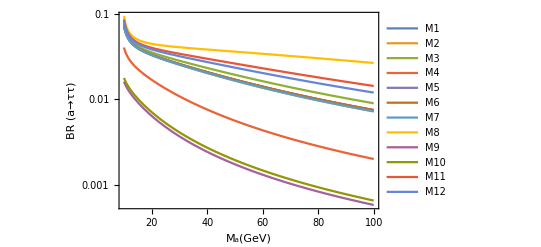

```mathematica
BRττplot = LogPlot[{BRττ/.M1,BRττ/.M2,BRττ/.M3,BRττ/.M4,BRττ/.M5,BRττ/.M6,BRττ/.M7,BRττ/.M8,BRττ/.M9,BRττ/.M10,BRττ/.M11,BRττ/.M12} , {Meta, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> ττ)},PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRtautau.eps",BRττplot]
```

BRtautau.eps

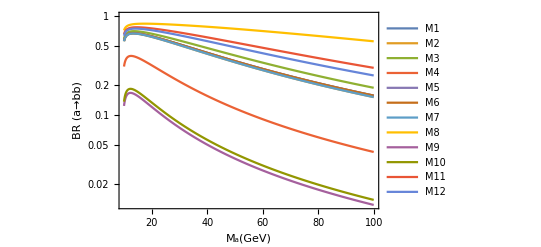

```mathematica
BRbbplot = LogPlot[{BRbb/.M1,BRbb/.M2,BRbb/.M3,BRbb/.M4,BRbb/.M5,BRbb/.M6,BRbb/.M7,BRbb/.M8,BRbb/.M9,BRbb/.M10,BRbb/.M11,BRbb/.M12} , {Meta, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> bb)},PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRbb.eps",BRbbplot]
```

BRbb.eps

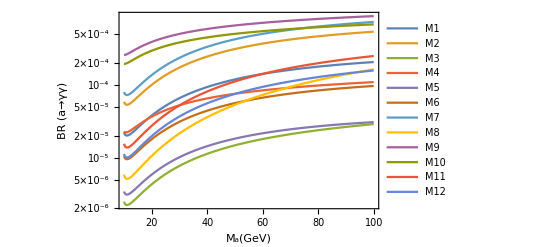

```mathematica
BRγγplot = LogPlot[{BRγγ/.M1,BRγγ/.M2,BRγγ/.M3,BRγγ/.M4,BRγγ/.M5,BRγγ/.M6,BRγγ/.M7,BRγγ/.M8,BRγγ/.M9,BRγγ/.M10,BRγγ/.M11,BRγγ/.M12} , {Meta, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> γγ)},PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRgammagamma.eps",BRγγplot]
```

BRgammagamma.eps

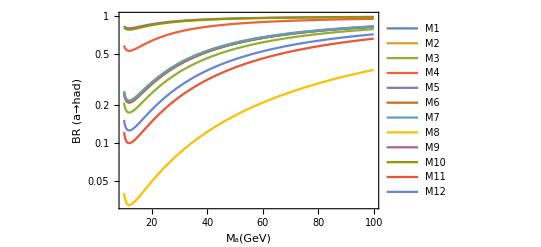

```mathematica
BRhadplot = LogPlot[{BRhad/.M1,BRhad/.M2,BRhad/.M3,BRhad/.M4,BRhad/.M5,BRhad/.M6,BRhad/.M7,BRhad/.M8,BRhad/.M9,BRhad/.M10,BRhad/.M11,BRhad/.M12} , {Meta, 10, 100},Frame -> True, FrameLabel->{Subscript[M, a][GeV],BR(a-> had)}, PlotLegends->{"M1", "M2", "M3", "M4", "M5", "M6", "M7", "M8", "M9", "M10", "M11", "M12"}]
```

```mathematica
Export["BRhad.eps",BRhadplot]
```

BRhad.eps

```mathematica
Assuming[Element[yd[__]|yu[__]|yl[__],Reals],
Simplify[FeynmanRules[
OptimizeIndex[ExpandIndices[LPSeudo + LSM]/.{(G0|GP|GPbar)->0}]
]/.{Eps[indx__]:>Signature[{indx}] Eps[Sequence@@Sort[{indx}]]}]
]
```

```mathematica
WriteFeynArtsOutput[LSM + LPSeudo, FlavorExpand->SU2W, FlavorExpand->SU2D]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: CHpseudo_FA

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

Warning: Class members in the Lagrangian! Not supported by FeynArts.

1 vertex obtained.

Redefining classes in such a way that each particle is in a separate FeynArts class.

See NewFeynArtsClasses[] for more information on the new classes

Restarting Feynman rule calculation, setting FlavorExpand -> True.

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

208 possible non-zero vertices have been found -> starting the computation:  / 208.

189 vertices obtained.

Writing FeynArts model file into directory CHpseudo_FA

Writing FeynArts generic file on CHpseudo_FA.gen.

```mathematica
<<FeynArts`
<< FormCalc`
model=FileNameJoin[{NotebookDirectory[],"CHpsuedo_FA","CHpseudo_FA"}];
```